# Linear protocol and counterdiabatic driving in STIRAP

```mathematica
ℏ = 1
Ωpi = 0.1
Ωpf = 10
ti = 0
Ωs[t_]:= 1.0
Ωp[t_, tf_]:=(Ωpf-Ωpi)*t/(tf-ti) + Ωpi
Δ = 0.1 
dΩp[t_,tf_]:=D[Ωp[b,tf],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_,tf_]:=2*(dΩp[t,tf]*Ωs[t]-Ωp[t,tf]*dΩs[t])/(Ωp[t,tf]^2 + Ωs[t]^2)
```

1

0.1

10

0

0.1

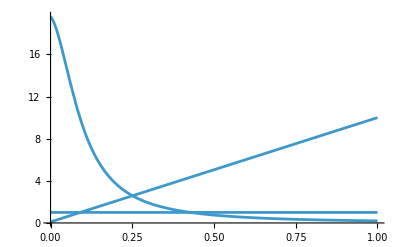

```mathematica
Show[Plot[Ωp[t,1.0],{t,ti,1.0}, PlotRange->All],
Plot[Ωs[t],{t,ti,1.0}],
Plot[Ωa[t,1.0],{t,ti,1.0}, PlotRange->All]]
```

```mathematica
(*Autovalores*)
Show[Plot[0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2], {t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Orange], Dashing[0.01]},FrameLabel ->{"t (μs)", "Eigenenergies / (ℏΩ_0)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_+(t)",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[-0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2], {t,ti,tf},PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> {Darker[Purple], DotDashed},FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_-(t)",10]},LegendLayout->"Row"],{Right,0.86}]], Plot[0,{t,ti,tf}, PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> Darker[Magenta],FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_0(t)",10]},LegendLayout->"Row"],{Right,0.78}]]]
```

Plot::plln: Limiting value tf in {t,0,tf} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Plot[0.5 √(Ωp[t,tf]^2+Ωs[t]^2),{t,ti,tf},PlotRange→All,PlotTheme→Detailed,PlotStyle→{Darker[Orange],Dashing[0.01]},FrameLabel→{t (μs),Eigenenergies / (ℏΩ_0)},LabelStyle→{Directive[11],FontFamily→Arial,Black},PlotLegends→Placed[LineLegend[{E_+(t)},LegendLayout→Row],{Right,0.94}]],«1»,Plot[0,{t,ti,tf},PlotRange→{-11,11},PlotTheme→Detailed,«9»→«1»,FrameLabel→{t (μs),E_+(t)},LabelStyle→{Directive[11],FontFamily→Arial,Black},PlotLegends→Placed[LineLegend[{E_0(t)},LegendLayout→Row],{Right,0.78}]]].

Show[Plot[0.5 √(Ωp[t,tf]^2+Ωs[t]^2),{t,ti,tf},PlotRange→All,PlotTheme→Detailed,PlotStyle→{Darker[Orange],Dashing[0.01]},FrameLabel→{t (μs),Eigenenergies / (ℏΩ_0)},LabelStyle→{Directive[11],FontFamily→Arial,Black},PlotLegends→Placed[LineLegend[{E_+(t)},LegendLayout→Row],{Right,0.94}]],Plot[-0.5 √(Ωp[t,tf]^2+Ωs[t]^2),{t,ti,tf},PlotRange→{-11,11},PlotTheme→Detailed,PlotStyle→{Darker[Purple],DotDashed},FrameLabel→{t (μs),E_+(t)},LabelStyle→{Directive[11],FontFamily→Arial,Black},PlotLegends→Placed[LineLegend[{E_-(t)},LegendLayout→Row],{Right,0.86}]],Plot[0,{t,ti,tf},PlotRange→{-11,11},PlotTheme→Detailed,PlotStyle→Darker[Magenta],FrameLabel→{t (μs),E_+(t)},LabelStyle→{Directive[11],FontFamily→Arial,Black},PlotLegends→Placed[LineLegend[{E_0(t)},LegendLayout→Row],{Right,0.78}]]]

```mathematica
time= Table[tf/2.198,{tf,Tmin,Tmax, ΔT}]
```

{0.0454959,5.09554,10.1456,15.1956,20.2457,25.2957,30.3458,35.3958,40.4459,45.4959}

```mathematica
Δ= 0.1
tf = 9.0
Tmin = 0.1
Tmax = 100
m = 9
ΔT = (Tmax-Tmin)/m
Sol = Table[NDSolve[{ⅈ*ℏ*c1'[t] ==(ℏ/2)*Ωp[t,tf]*c2[t],ⅈ*ℏ*c2'[t] ==(ℏ/2)*Ωp[t,tf]*c1[t]+(ℏ/2)*Δ*c2[t]+ (ℏ/2)*Ωs[t]*c3[t],ⅈ*ℏ*c3'[t] ==+(ℏ/2)*Ωs[t]*c2[t],c1[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ],c2[ti]==0,c3[ti]==-Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ] },{c1,c2,c3},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
SolCD = Table[NDSolve[{ⅈ*ℏ*c1CD'[t] ==(ℏ/2)*Ωp[t,tf]*c2CD[t]+ⅈ*(ℏ/2)*Ωa[t,tf]*c3CD[t],ⅈ*ℏ*c2CD'[t] ==(ℏ/2)*Ωp[t,tf]*c1CD[t]+(ℏ/2)*Δ*c2CD[t]+(ℏ/2)*Ωs[t]*c3CD[t],ⅈ*ℏ*c3CD'[t] ==-ⅈ*(ℏ/2)*Ωa[t,tf]*c1CD[t]+(ℏ/2)*Ωs[t]*c2CD[t],c1CD[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ],c2CD[ti]==0,c3CD[ti]==-Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ] },{c1CD,c2CD,c3CD},{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

0.1

9.

0.1

100

9

11.1

{{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}}}

{{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}}}

```mathematica
(*Probabilities |1 >*)
p1 = Table[Abs[c1[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
p2 = Table[Abs[c2[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
p3 = Table[Abs[c3[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pCD1 = Table[Abs[c1CD[t]/.Part[Flatten[Part[SolCD,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pCD2 = Table[Abs[c2CD[t]/.Part[Flatten[Part[SolCD,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pCD3 = Table[Abs[c3CD[t]/.Part[Flatten[Part[SolCD,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.929907,0.372193,0.204554,0.00211636,0.0219079,0.10104,0.104504,0.0446412,0.0213702,0.0251801}

{0.0593618,0.112802,0.224921,0.24218,0.151785,0.0424904,0.000391703,0.0229252,0.0488444,0.0390973}

{0.0107307,0.515003,0.570525,0.755704,0.826308,0.85647,0.895105,0.932435,0.929787,0.935724}

{0.00990098,0.00990098,0.00990099,0.00990098,0.00990098,0.00990099,0.00990099,0.00990099,0.00990099,0.00990099}

{6.91131×10^-18,2.09979×10^-15,5.52397×10^-15,8.73549×10^-17,9.46846×10^-17,1.36062×10^-16,3.95733×10^-16,7.24773×10^-17,2.03277×10^-16,2.3939×10^-17}

{0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099}

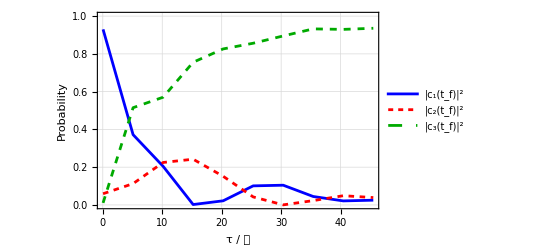

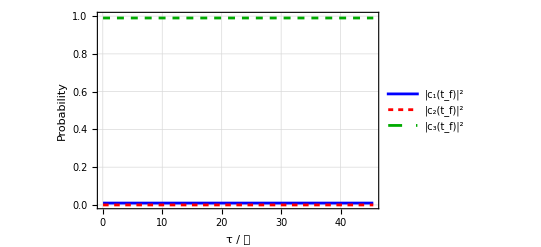

```mathematica
gLIN = Show[ListPlot[Transpose[{time,p1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,p2}], PlotStyle->{Red, Dashing[0.01]}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,p3}], PlotStyle->{Darker[Green], Dashed}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
gCD = Show[ListPlot[Transpose[{time,pCD1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pCD2}], PlotStyle->{Red, Dashing[0.01]}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pCD3}], PlotStyle->{Darker[Green], Dashed}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Minimal action

```mathematica
ProtMA = Table[NDSolve[{D[ΩpMA'[t]/(ΩpMA[t]^2 + Ωs[t]^2),t] + 4*Δ/(ΩpMA[t]^2 + Ωs[t]^2)^(3/2)*(ΩpMA''[t] - 2.5*ΩpMA[t]*ΩpMA'[t]^2/(ΩpMA[t]^2 + Ωs[t]^2)) ==0 , ΩpMA[ti]==Ωpi, ΩpMA[tf]==Ωpf},ΩpMA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}}}

```mathematica
Flatten[Part[ProtMA,1]]
```

{ΩpMA→InterpolatingFunction[…]}

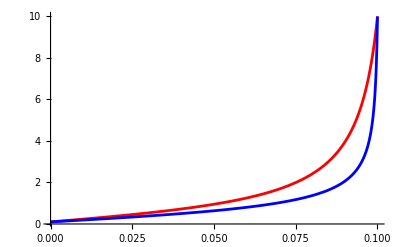

```mathematica
Show[Plot[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,1]]],{t,ti,0.1}, PlotRange->All, PlotStyle->Red], Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,1]]],{t,ti,0.1}, PlotRange->All, PlotStyle->Blue]]
```

```mathematica
SolMA = Table[NDSolve[{ⅈ*ℏ*c1MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c2MA[t],ⅈ*ℏ*c2MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c1MA[t]+(ℏ/2)*Δ*c2MA[t]+ (ℏ/2)*Ωs[t]*c3MA[t],ⅈ*ℏ*c3MA'[t] ==+(ℏ/2)*Ωs[t]*c2MA[t],c1MA[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2MA[ti]==0,c3MA[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1MA,c2MA,c3MA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}}}

```mathematica
pMA1 = Table[Abs[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA2 = Table[Abs[c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA3 = Table[Abs[c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.984324,0.0107227,0.00323732,0.0133057,0.0182923,0.0106757,0.0103394,0.0133311,0.0107533,0.00697127}

{0.00561012,0.0140692,0.00633096,0.00670444,0.000139075,0.00154227,0.00103779,0.0000810316,0.000729687,0.00012012}

{0.0100656,0.975209,0.990431,0.97999,0.981568,0.987782,0.988623,0.986588,0.988517,0.992908}

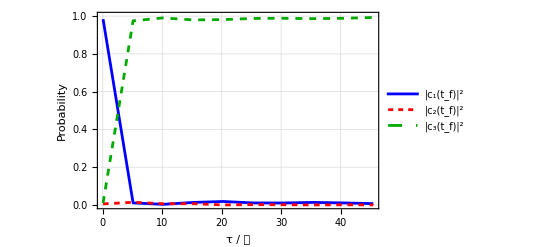

```mathematica
gMA = Show[ListPlot[Transpose[{time,pMA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pMA2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pMA3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Fast quasidiabatic

```mathematica
ProtFQ = Table[NDSolve[{D[ΩpFQ'[t]/(ΩpFQ[t]^2 + Ωs[t]^2)^(3/2)*(1+1.5*Δ/(ΩpFQ[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ[ti]==Ωpi, ΩpFQ[tf]==Ωpf},ΩpFQ,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}}}

```mathematica
SolFQ = Table[NDSolve[{ⅈ*ℏ*c1FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c2FQ[t],ⅈ*ℏ*c2FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c1FQ[t]+(ℏ/2)*Δ*c2FQ[t]+ (ℏ/2)*Ωs[t]*c3FQ[t],ⅈ*ℏ*c3FQ'[t] ==+(ℏ/2)*Ωs[t]*c2FQ[t],c1FQ[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2FQ[ti]==0,c3FQ[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1FQ,c2FQ,c3FQ},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}}}

```mathematica
pFQ1 = Table[Abs[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ2 = Table[Abs[c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ3 = Table[Abs[c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.988126,0.0459626,0.00320004,0.0101895,0.0140207,0.0098961,0.00948236,0.00909464,0.0124408,0.00954368}

{0.00187438,0.0701052,0.0135159,0.00199748,0.00317591,0.00173687,0.00168048,0.000505305,0.000380384,0.00123236}

{0.00999996,0.883931,0.983284,0.987813,0.982803,0.988367,0.988837,0.9904,0.987179,0.989224}

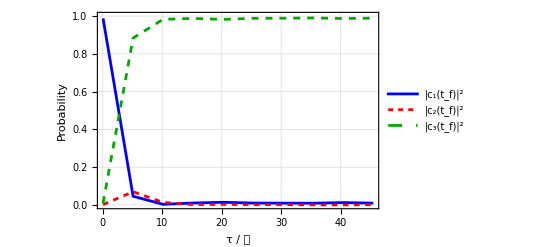

```mathematica
gFQ = Show[ListPlot[Transpose[{time,pFQ1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pFQ2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pFQ3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

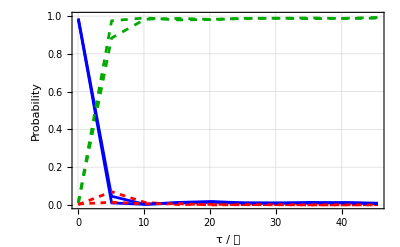

```mathematica
Show[gFQ,gMA]
```

## Boundary cancellation method

```mathematica
ΩpBCM[t_,tf_]:= Ωpi + ( Ωpf- Ωpi)*(3*((t-ti)/(tf-ti))^2 - 2*((t-ti)/(tf-ti))^3)
```

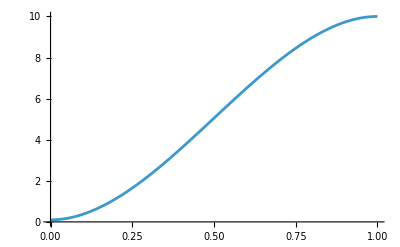

```mathematica
Plot[ΩpBCM[t,1.0],{t,ti,1.0}]
```

```mathematica
SolBCM = Table[NDSolve[{ⅈ*ℏ*c1BCM'[t] ==(ℏ/2)*ΩpBCM[t,tf]*c2BCM[t],ⅈ*ℏ*c2BCM'[t] ==(ℏ/2)*ΩpBCM[t,tf]*c1BCM[t]+(ℏ/2)*Δ*c2BCM[t]+ (ℏ/2)*Ωs[t]*c3BCM[t],ⅈ*ℏ*c3BCM'[t] ==+(ℏ/2)*Ωs[t]*c2BCM[t],c1BCM[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2BCM[ti]==0,c3BCM[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1BCM,c2BCM,c3BCM},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}}}

```mathematica
pBCM1 = Table[Abs[c1BCM[t]/.Part[Flatten[Part[SolBCM,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pBCM2 = Table[Abs[c2BCM[t]/.Part[Flatten[Part[SolBCM,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pBCM3 = Table[Abs[c3BCM[t]/.Part[Flatten[Part[SolBCM,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.929983,0.382586,0.228104,0.00787321,0.0124828,0.0192743,0.0161918,0.0101139,0.00803851,0.0140313}

{0.0593705,0.0465127,0.0838835,0.0815308,0.0414159,0.00862818,0.000189909,0.0013192,0.000879265,0.0000301364}

{0.0106462,0.570901,0.688013,0.910597,0.946102,0.972098,0.983618,0.988566,0.991082,0.985938}

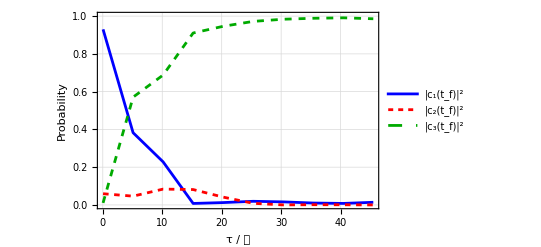

```mathematica
gBCM = Show[ListPlot[Transpose[{time,pBCM1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pBCM2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pBCM3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

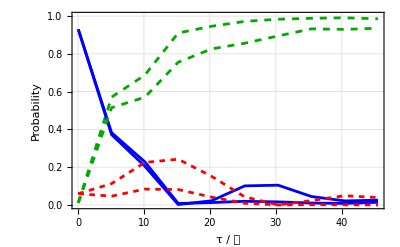

```mathematica
Show[gBCM,gLIN]
```

## Optimal time-averaged excess work

## Uniform adiabatic

```mathematica
ProtFQ = Table[NDSolve[{D[ΩpFQ'[t]/(ΩpFQ[t]^2 + Ωs[t]^2)^(3/2)*(1+1.5*Δ/(ΩpFQ[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ[ti]==Ωpi, ΩpFQ[tf]==Ωpf},ΩpFQ,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```